## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.21075 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 27, 2020, time: 00:53:36

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/34-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.21075 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

```mathematica
𝕔=299792458;
```

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
fticks={{Automatic,Automatic},{θticks,Automatic}};
```

#### functions

#### substitutions

#### modules

## raw data

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=meanRCS[[1]];
{M,𝒩}=Dimensions[meanRCS]
```

{28,361}

```mathematica
S=meanRCSᵀ;
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## plot

```mathematica
plot3=ListPlot[meanRCS[[1]],Joined->True,PlotStyle->Black];
plot4=ListPlot[meanRCS[[2]],Joined->True,PlotStyle->Blue];
Show[{plot3,plot4},
ipad,
Frame->True,
PlotRange->All]
```

```mathematica
plot29=ListPlot[meanRCS[[27]],Joined->True,PlotStyle->Black];
plot30=ListPlot[meanRCS[[28]],Joined->True,PlotStyle->Blue];
Show[{plot29,plot30},
ipad,
Frame->True,
PlotRange->Full]
```

```mathematica
Show[{plot3,plot4,plot29,plot30},
ipad,
Frame->True,
PlotRange->Full]
```

```mathematica
ListPlot[meanRCS[[1]]-meanRCS[[2]]]
```

```mathematica
ListPlot[meanRCS[[27]]-meanRCS[[28]],Joined->True]
```

```mathematica
fticks
```

{{Automatic,Automatic},{{{1,-180°},{91,-90°},{181,0°},{271,90°},{361,180°}},Automatic}}

```mathematica
g1=ListPlot[meanRCS[[1]],PlotStyle->{Black,PointSize[0.0075]}];
```

```mathematica
gall=ListPlot[meanRCS,
ipad,
Frame->True,
PlotLabel->"Radar Frequency ν = 3, 4, ..., 30 MHz",
FrameTicks->{{Automatic,Automatic},{{{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}},Automatic}},
FrameLabel->{"Yaw angle","Total Mean RCS, sq m"}];
g001=Show[{gall,g1}]
```

```mathematica
ν=Range[3,30]1000000;
λ=𝕔/ν;
```

```mathematica
Λ={Range[3,30],λ}ᵀ;
```

```mathematica
g002=BarChart[λ,
ipad,
ChartStyle->{{Blue},{Opacity[0.1]}},
PlotLabel->"Radar Frequency and Wavelength",
FrameLabel->{"Radar Frequency, MHz","Radar Wavelength, m"},
FrameTicks->{{Automatic,Automatic},{{{1,3},{2,4},{8,10},{18,20},{28,30}},Automatic}},
Frame->True]
```

```mathematica
gr=Graphics[{Red,Opacity[0.25],Rectangle[{-1,λ[[1]]},{33,λ[[2]]}]}];
```

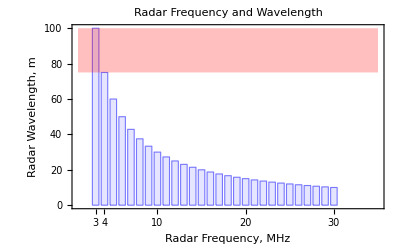

```mathematica
g100=Show[{g002,gr}]
```

```mathematica
tresExport["z-rcs",g100]
tresExport["z-hyperbolic",g001]
```

```mathematica
λ[[1]]-λ[[2]]//N
```

24.9827

```mathematica
λ[[1]]//N
```

99.9308

```mathematica
BarChart[λ,
ipad,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameLabel->{"Radar Frequency, MHz","Radar Wavelength, m"},
FrameTicks->{{Automatic,Automatic},{{{1,3},{2,4},{8,10},{18,20},{28,30}},Automatic}},
Frame->True]
```

```mathematica
Table[Black,{1}]
```

{GrayLevel[0]}

```mathematica
BarChart[λ,
ipad,
ChartStyle->{{Blue},{Opacity[0.1]}},
PlotRange->{Automatic,{20,100}},
FrameLabel->{"Radar Frequency, MHz","Radar Wavelength, m"},
FrameTicks->{{Automatic,Automatic},{{{1,3},{2,4},{8,10},{18,20},{28,30}},Automatic}},
Frame->True]
```

```mathematica
Last[λ]//N
```

9.99308

```mathematica
gb=BarChart[Take[Λ,2],
ChartStyle->{{Blue},{Opacity[0.25]}}]
```

```mathematica
ga=BarChart[Drop[λ,2],
ChartStyle->{{Blue},{Opacity[0.05]}}]
```

```mathematica
Show[{ga,gb}]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```